### Define Log0

```mathematica
Clear[Arg0,Log0];

(*Arg in[0,2π)–cut on positive real axis*)
Arg0[z_?NumericQ]:=Module[{θ=Arg[z]},If[θ<0,θ+2 Pi,θ]];

(*Custom logarithm with that Arg*)
Log0[z_?NumericQ]:=Log[Abs[z]]+I Arg0[z];

(*For symbolic z:treat Log0 as ordinary Log Log0[z_]/;!NumericQ[z]:=Log[z];*)


ArcTanh0[z_?NumericQ]:=(Log0[1+z]-Log0[1-z])/2;
```

### HLog

```mathematica
HLog[r_,r0_]:=1+ I/Pi Log[r-r0]
```

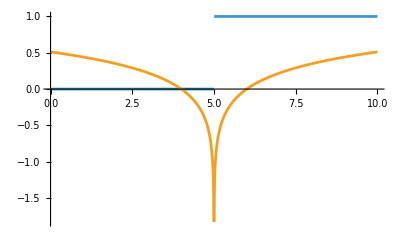

```mathematica
Plot[{Re@HLog[r,5],Im@HLog[r,5]},{r,0,10}]
```

```mathematica
Integrate[HLog[r,r0],r]//FullSimplify
```

((-ⅈ+π) r+ⅈ (r-r0) Log[r-r0])/π

```mathematica
Kink[r_,r0_]:=((-ⅈ+π) r+ⅈ (r-r0) Log[r-r0])/π
```

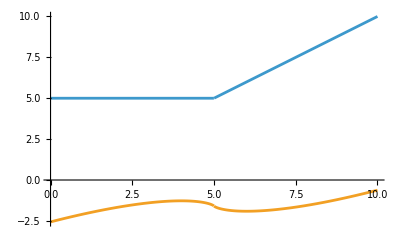

```mathematica
Plot[{Re@Kink[r,5],Im@Kink[r,5]},{r,0,10}]
```

```mathematica
D[HeavisideTheta[r-r0],r]
```

DiracDelta[r-r0]

```mathematica
D[HLog[r,r0],r]
```

ⅈ/(π (r-r0))

```mathematica
ExtendedDiracDelta[r_,r0_]:=ⅈ/(π (r-r0))
```

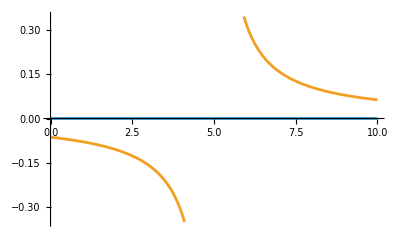

```mathematica
Plot[{Re@ExtendedDiracDelta[r,5],Im@ExtendedDiracDelta[r,5]},{r,0,10}]
```

### HLog0 (no different)

```mathematica
HLog0[r_,r0_]:=1+ I/Pi Log0[r-r0]
```

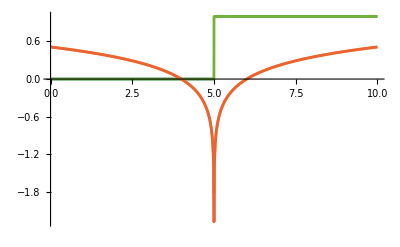

```mathematica
Plot[{Re@HLog[r,5],Im@HLog[r,5],Re@HLog0[r,5],Im@HLog0[r,5]},{r,0,10}]
```

```mathematica
Integrate[HLog0[r,r0],r]//FullSimplify
```

∫(1+(ⅈ Log0[r-r0])/π)ⅆr

### Contour

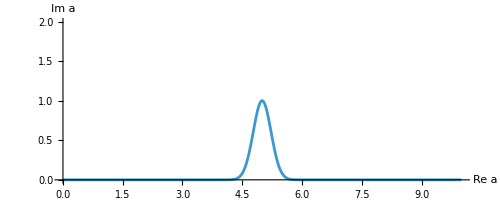

```mathematica
z0=5; (*position of source peak*)
J=1;  (*Gaussian height*)

(*Contour definition*)γ[a_]:=a+I J Exp[-10 (a-z0)^(2)];
γp[a_]:=D[γ[a],a];
γpp[a_]:=D[γ[a],{a,2}];

(*Plot in the complex plane,clipping the huge tails in Im[z]*)
ParametricPlot[{Re[γ[a]],Im[γ[a]]},{a,0,10},AxesLabel->{"Re a","Im a"},PlotRange->{All,{0,2}}]
```

### Integrate HLog along Contour

```mathematica
(*Clear previous definitions*)ClearAll[HLog,ExtendedDelta,r,r0,z,t];

(*1. Define the Complex Heaviside Function*)
HLog[r_,r0_]:=1+I/Pi Log[r-r0];

(*2. Derive the Extended Dirac Delta*)
ExtendedDelta[r_,r0_]=D[HLog[r,r0],r];

Print["The extended Dirac Delta is analytically defined as: ",ExtendedDelta[r,r0]]

(*3. Symbolic Indefinite Integration*)
(*We check if Mathematica recovers the Log term symbolically*)
symbolicIntegral=Integrate[ExtendedDelta[r,r0],r];
Print["Symbolic indefinite integral yields: ",symbolicIntegral]
```

The extended Dirac Delta is analytically defined as: ⅈ/(π (r-r0))

Symbolic indefinite integral yields: (ⅈ Log[π r-π r0])/π

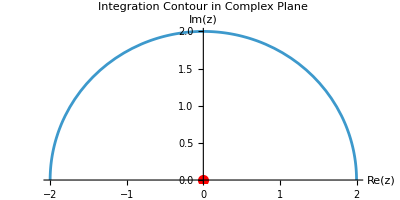

```mathematica
(*4. Set parameters for the contour*)r0Val=0;
rStart=-2.0;
rEnd=2.0;

(*Parameterize a semi-circle in the upper half-plane from-1 to 1*)
(*As t goes from 0 to 1,the angle goes from Pi to 0*)
contour[t_]:=2Exp[I Pi (1-t)];

(*Plot the contour to verify the path avoids the origin*)
ParametricPlot[{Re[contour[t]],Im[contour[t]]},{t,0,1},AxesLabel->{"Re(z)","Im(z)"},PlotLabel->"Integration Contour in Complex Plane",Epilog->{Red,PointSize[0.02],Point[{0,0}],Text["Singularity r0",{0,-0.1}]}]
```

```mathematica
(*5. Perform the contour integration numerically*)(*dz=D[contour[t],t] dt*)contourIntegral=NIntegrate[Evaluate[ExtendedDelta[contour[t],r0Val]*D[contour[t],t]],{t,0,1}];

Print["Result of Contour Integration: ",Chop[contourIntegral]]

(*6. Evaluate the endpoints using the proposed HLog function*)
(*Note:Log[-1] in Mathematica evaluates to I Pi*)
HeavisideDiff=HLog[rEnd,r0Val]-HLog[rStart,r0Val];

Print["Result of HLog[1] - HLog[-1]: ",Simplify[HeavisideDiff]]

(*7. Verification check*)
If[Abs[contourIntegral-HeavisideDiff]<10^-10,Print["Success: The contour integral matches the HLog boundary values!"],Print["Warning: Mismatch detected."]]
```

NIntegrate::inumr: The integrand -ⅈ ⅇ^(ⅈ π (1-t)) π ExtendedDelta[ⅇ^(ⅈ π (1-t)),0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

Result of Contour Integration: NIntegrate[-ⅈ ⅇ^(ⅈ π (1-t)) π ExtendedDelta[ⅇ^(ⅈ π (1-t)),0],{t,0,1}]

Result of HLog[1] - HLog[-1]: -HLog[-2.,0]+HLog[2.,0]

NIntegrate::inumr: The integrand -ⅈ ⅇ^(ⅈ π (1-t)) π ExtendedDelta[ⅇ^(ⅈ π (1-t)),0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

If[Abs[HLog[-2.,0]-HLog[2.,0]+NIntegrate[-ⅈ ⅇ^(ⅈ π (1-t)) π ExtendedDelta[ⅇ^(ⅈ π (1-t)),0],{t,0,1}]]<1/10000000000,Print[Success: The contour integral matches the HLog boundary values!],Print[Warning: Mismatch detected.]]

```mathematica
contourIntegral
```

1.

Initial value HLog[-1] is: (ⅈ Log[2])/π

Maximum numerical deviation along the contour: 2.23773×10^-16

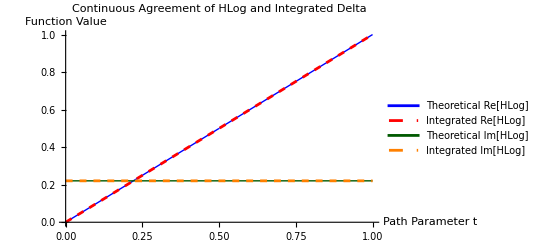

```mathematica
(*1. Initialization and Definitions*)ClearAll[HLog,ExtendedDelta,contour,t];

(*Define the theoretical functions*)
HLog[z_]:=1+I/Pi Log[z];
ExtendedDelta[z_]:=I/(Pi z);

(*Define the semi-circular contour from z=-1 to z=1*)
contour[t_]:=2Exp[I Pi (1-t)];

(*2. Initial Condition Formulation*)
(*The starting value of the integral must match the function at t=0*)
initialValue=HLog[contour[0]];
Print["Initial value HLog[-1] is: ",Simplify[initialValue]];

(*3. Differential Equation Setup for the Contour Integral*)
(*We use NDSolveValue to sweep the integral along the contour continuously*)
integratedHLog=NDSolveValue[{y'[t]==ExtendedDelta[contour[t]]*contour'[t],y[0]==initialValue},y,{t,0,1}];

(*4. Compute Maximum Error*)
(*We sample the difference between the integrated result and the theoretical function*)
errorArray=Table[Abs[integratedHLog[t]-HLog[contour[t]]],{t,0,1,0.01}];
Print["Maximum numerical deviation along the contour: ",Max[errorArray]];

(*5. Visualization of the Match*)
(*We plot the Real and Imaginary parts of both functions.The Dashed lines (Integrated) will perfectly overlay the Thick lines (Theoretical).*)
Plot[{Re[HLog[contour[t]]],Re[integratedHLog[t]],Im[HLog[contour[t]]],Im[integratedHLog[t]]},{t,0,1},PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed],Directive[DarkGreen,Thick],Directive[Orange,Dashed]},PlotLegends->{"Theoretical Re[HLog]","Integrated Re[HLog]","Theoretical Im[HLog]","Integrated Im[HLog]"},AxesLabel->{"Path Parameter t","Function Value"},PlotLabel->"Continuous Agreement of HLog and Integrated Delta"]
```

```mathematica
HLog[2]
```

1+(ⅈ Log[2])/π

```mathematica
HLog[I]//N
```

0.5

```mathematica
contour[0.5]
```

6.12323×10^-17+1. ⅈ

```mathematica
HLog[%]
```

0.5+0. ⅈ

```mathematica
Im[HLog[contour[0.5]]]
```

0.

```mathematica
(*1. Clear symbols to prevent conflicts*)ClearAll[HLog,ExtendedDelta,contour,t,r0Val,rStart,rEnd,R];

(*2. Define the Functions*)
HLog[r_,r0_]:=1+I/Pi Log[r-r0];
ExtendedDelta[r_,r0_]:=I/(Pi (r-r0));

(*3. Set parameters for the expanded contour*)
r0Val=0;
R=2.0; (*Radius of the semi-circle*)
rStart=-R;
rEnd=R;

(*Parameterize a semi-circle of radius R*)
contour[t_]:=R Exp[I Pi (1-t)];

(*4. Perform the contour integration numerically*)
contourIntegral=NIntegrate[Evaluate[ExtendedDelta[contour[t],r0Val]*D[contour[t],t]],{t,0,1}];

Print["Result of Contour Integration: ",Chop[contourIntegral]];

(*5. Evaluate the endpoints using the HLog function*)
HeavisideDiff=HLog[rEnd,r0Val]-HLog[rStart,r0Val];

Print["Result of HLog[",rEnd,"] - HLog[",rStart,"]: ",Simplify[HeavisideDiff]];

(*6. Verification check*)
If[Abs[contourIntegral-HeavisideDiff]<10^-10,Print["Success: The contour integral matches the HLog boundary values!"],Print["Warning: Mismatch detected."]]
```

Result of Contour Integration: 1.

Result of HLog[2.] - HLog[-2.]: 1.+0. ⅈ

Success: The contour integral matches the HLog boundary values!

```mathematica
(*1. Initialization and Definitions*)ClearAll[HLog,ExtendedDelta,contour,t];

(*Define the theoretical functions*)
HLog[z_]:=1+I/Pi Log[z];
ExtendedDelta[z_]:=I/(Pi z);

(*Define the semi-circular contour from z=-1 to z=1*)
contour[t_]:=2Exp[I Pi (1-t)];

(*2. Initial Condition Formulation*)
(*The starting value of the integral must match the function at t=0*)
initialValue=HLog[contour[0]];
Print["Initial value HLog[-1] is: ",Simplify[initialValue]];

(*3. Differential Equation Setup for the Contour Integral*)
(*We use NDSolveValue to sweep the integral along the contour continuously*)
integratedHLog=NDSolveValue[{y'[t]==ExtendedDelta[contour[t]]*contour'[t],y[0]==initialValue},y,{t,0,1}];

(*4. Compute Maximum Error*)
(*We sample the difference between the integrated result and the theoretical function*)
errorArray=Table[Abs[integratedHLog[t]-HLog[contour[t]]],{t,0,1,0.01}];
Print["Maximum numerical deviation along the contour: ",Max[errorArray]];

(*5. Visualization of the Match*)
(*We plot the Real and Imaginary parts of both functions.The Dashed lines (Integrated) will perfectly overlay the Thick lines (Theoretical).*)
Plot[{Re[HLog[contour[t]]],Re[integratedHLog[t]],Im[HLog[contour[t]]],Im[integratedHLog[t]]},{t,0,1},PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed],Directive[DarkGreen,Thick],Directive[Orange,Dashed]},PlotLegends->{"Theoretical Re[HLog]","Integrated Re[HLog]","Theoretical Im[HLog]","Integrated Im[HLog]"},AxesLabel->{"Path Parameter t","Function Value"},PlotLabel->"Continuous Agreement of HLog and Integrated Delta"]
```

Initial value HLog[-1] is: (ⅈ Log[2])/π

Maximum numerical deviation along the contour: 2.23773×10^-16

-Graphics-

Initial value HLog[-1] is: 1.5+0.220636 ⅈ

Maximum numerical deviation along the contour: 2.

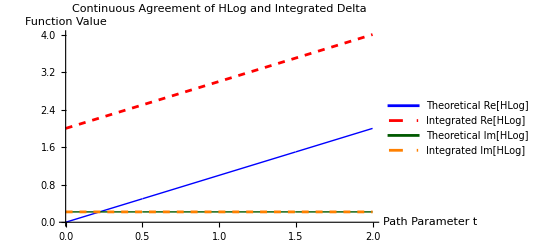

```mathematica
(*1. Initialization and Definitions*)ClearAll[HLog,ExtendedDelta,contour,t];

(*Define the theoretical functions*)
HLog[z_]:=1+I/Pi Log[z];
ExtendedDelta[z_]:=I/(Pi z);

(*Define the semi-circular contour from z=-1 to z=1*)
contour[t_]:=2Exp[I Pi (1-t)];

(*2. Initial Condition Formulation*)
(*The starting value of the integral must match the function at t=0*)
initialValue=HLog[contour[-0.5]];
Print["Initial value HLog[-1] is: ",Simplify[initialValue]];

(*3. Differential Equation Setup for the Contour Integral*)
(*We use NDSolveValue to sweep the integral along the contour continuously*)
integratedHLog=NDSolveValue[{y'[t]==ExtendedDelta[contour[t]]*contour'[t],y[-0.5]==initialValue},y,{t,0,1}];

(*4. Compute Maximum Error*)
(*We sample the difference between the integrated result and the theoretical function*)
errorArray=Table[Abs[integratedHLog[t]-HLog[contour[t]]],{t,0,1,0.01}];
Print["Maximum numerical deviation along the contour: ",Max[errorArray]];

(*5. Visualization of the Match*)
(*We plot the Real and Imaginary parts of both functions.The Dashed lines (Integrated) will perfectly overlay the Thick lines (Theoretical).*)
Plot[{Re[HLog[contour[t]]],Re[integratedHLog[t]],Im[HLog[contour[t]]],Im[integratedHLog[t]]},{t,0,2},PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed],Directive[DarkGreen,Thick],Directive[Orange,Dashed]},PlotLegends->{"Theoretical Re[HLog]","Integrated Re[HLog]","Theoretical Im[HLog]","Integrated Im[HLog]"},AxesLabel->{"Path Parameter t","Function Value"},PlotLabel->"Continuous Agreement of HLog and Integrated Delta"]
```

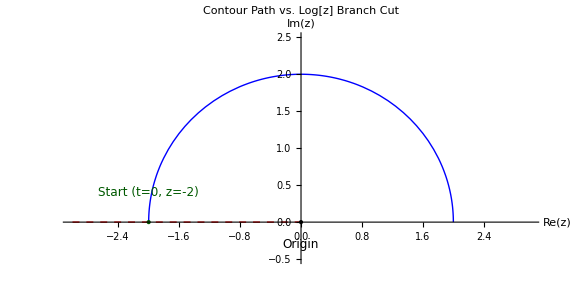

```mathematica
(*1. Define the contour exactly as in your notebook*)contour[t_]:=2 Exp[I Pi (1-t)];

(*2. Define the branch cut for the principal Log[z] (negative real axis)*)
branchCut=Line[{{-3,0},{0,0}}];

(*3. Visualize the complex plane*)
ParametricPlot[{Re[contour[t]],Im[contour[t]]},{t,0,1},PlotStyle->Directive[Blue,Thick],(*Add the branch cut,origin,and the starting point of the contour*)Epilog->{Directive[Red,Thick,Dashed],branchCut,Directive[Black,PointSize[Large]],Point[{0,0}],Text[Style["Origin",12,Black,Background->White],{0,-0.3}],Directive[DarkGreen,PointSize[Large]],Point[{Re[contour[0]],Im[contour[0]]}],Text[Style["Start (t=0, z=-2)",12,DarkGreen,Background->White],{-2,0.4}]},PlotRange->{{-3,3},{-0.5,2.5}},AxesLabel->{"Re(z)","Im(z)"},PlotLabel->Style["Contour Path vs. Log[z] Branch Cut",14,Bold],ImageSize->Large]
```